```mathematica
(* L1-norm calculation for MEMS-state under correlated-depolarizing channel with memory: *)
```

```mathematica
(* Defining uncorrelated-depolarizing channel Kraus Operators for single qubit: *)
SetDirectory[NotebookDirectory[]];
ClearAll[g,γ, μ,  p];
$Assumptions=p ≥  0 && √(1-p)≥ 0 && Element[√(1-p),Reals];
E0=√(1-p) PauliMatrix[0];
E1=√(p/3) PauliMatrix[1];
E2=√(p/3) PauliMatrix[2];
E3=√(p/3) PauliMatrix[3];
Es={{E0,E1,E2,E3}};

(* Checking the completenes condition:*)
 FullSimplify[Sum[ConjugateTranspose[Es[[1,i]]]. Es[[1,i]],{i,1,4}]]//MatrixForm ;

(* Uncorrelated-Depolarizing channel Kraus operators for two-qubits:  *)
 eu=Table[KroneckerProduct[Es[[1,i]],Es[[1,j]]],{i,1,4},{j,1,4}] ;

(* Correlated-depolarizing channel Kraus operators for two qubits: *)
ec0 =√(1-p) KroneckerProduct[PauliMatrix[0],PauliMatrix[0]] ;
ec1 =√(p/3)  KroneckerProduct[PauliMatrix[1],PauliMatrix[1]] ;
ec2 =√(p/3) KroneckerProduct[PauliMatrix[2],PauliMatrix[2]] ;
ec3 =√(p/3) KroneckerProduct[PauliMatrix[3],PauliMatrix[3]] ;
ec={{ec0, ec1, ec2, ec3}};

(* Checking the completeness of the Kraus operators: *)
FullSimplify[Sum[ConjugateTranspose[eu[[i,j]]].eu[[i,j]],{i,1,4},{j,1,4}]]//MatrixForm;
FullSimplify[Sum[ConjugateTranspose[ec[[1,i]]].ec[[1,i]],{i,1,4}]]//MatrixForm;
```

```mathematica
(* MEMS-state density Matrix *)
ClearAll[g,γ,p,μ];
 ρ={{g,0,0,γ/2},{0,1-2g,0,0},{0,0,0,0},{γ/2,0,0,g}};
ρ//MatrixForm;
Tr[ρ];

(* Density Matrix after evolution in ADC: *)
ρ2=(1-μ)*Sum[eu[[i,j]].ρ.ConjugateTranspose[eu[[i,j]]],{i,1,4},{j,1,4}]+μ*Sum[ec[[1,i]].ρ.ConjugateTranspose[ec[[1,i]]],{i,1,4}]; 

Simplify[Tr[ρ2]];
FullSimplify[ρ2]//MatrixForm;
```

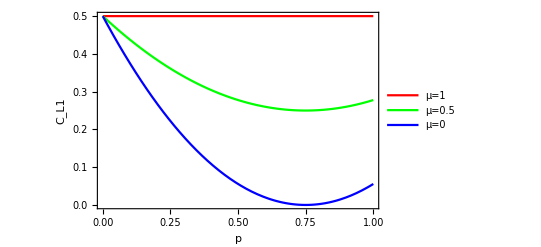

```mathematica
(* L1-norm of coherence for MEMS state: γ < 2/3 *)
ClearAll[g,γ, μ,  p];
γ=0.5;
g=1/3;
L1=Sum[If[i!=j,Abs[ρ2[[i,j]]],0],{i,1,4},{j,1,4}];
L1fig1=Plot[Evaluate@Table[L1,{μ,{1,0.5,0}}],{p,0,1},FrameLabel->{"p","C_L1"},PlotLegends->Placed[LineLegend[{"μ=1", "μ=0.5","μ=0"}],{0.9,0.75}],PlotStyle->{Red, Green, Blue},Frame-> True, FrameStyle->Directive[Black,12]]

(* Export the plot to the NotebookDirectory. In the Export[] function, change the figure extension '.pdf' to '.jpg' or '.png' as you need. *)
Export["L1fig1_DepCh.pdf",L1fig1];
```

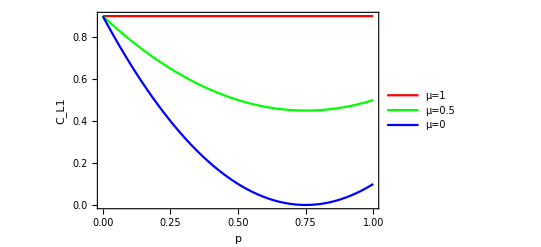

```mathematica
(*L1-norm of coherence for MEMS state: γ>2/3 *)
ClearAll[g,γ, μ,  p];
γ=0.9;
g=γ/2;
L1=Sum[If[i!=j,Abs[ρ2[[i,j]]],0],{i,1,4},{j,1,4}];
L1fig2=Plot[Evaluate@Table[L1,{μ,{1,0.5,0}}],{p,0,1},FrameLabel->{"p","C_L1"},PlotLegends->Placed[LineLegend[{"μ=1", "μ=0.5","μ=0"}],{0.9,0.75}],PlotStyle->{Red, Green, Blue},Frame-> True, FrameStyle->Directive[Black,12]]

Export["L1fig2_DepCh.pdf",L1fig2];
```

```mathematica
(* L1-norm in 3D plot *)
ClearAll[g,γ, μ,  p];
γ=0.5;
g=1/3;
L1=Sum[If[i!=j,Abs[ρ2[[i,j]]],0],{i,1,4},{j,1,4}];
L1norm3D=Plot3D[L1,{p,0,1},{μ,0,1},AxesLabel->{"p","μ","C_L1 "},AxesStyle->Directive[Bold,Black, 12],ColorFunction->Function[{x,y,z},Hue[Mod[z,1]]],ColorFunctionScaling->False]
Export["L1norm3D_DepCh.pdf",L1norm3D];
```

-Graphics3D-

```mathematica
(* Concurrence Module: *)
rhotilde[state_]:=(KroneckerProduct[PauliMatrix[2],PauliMatrix[2]]).(Conjugate[state].(KroneckerProduct[PauliMatrix[2],PauliMatrix[2]]));
  rhocon[state_]:=state.rhotilde[state];
eigensqrt[state_]:=Re[Sqrt[Eigenvalues[rhocon[state]]]];
order[state_]:=Sort[eigensqrt[state],Greater];
concurr[state_]:=Max[0,order[state][[1]]-order[state][[2]]-order[state][[3]]-order[state][[4]]];
```

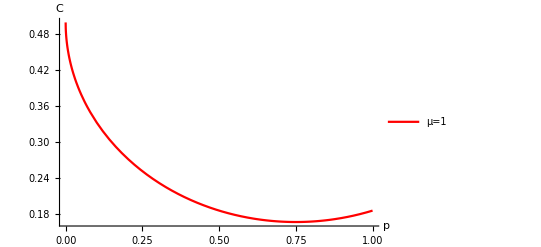

```mathematica
ClearAll[g,γ, μ,  p];
γ=0.5;
g=1/3;
μ=1;
p1=Plot[N[concurr[ρ2]],{p,0,1},AxesLabel->{"p","C"},PlotRange->All,AxesOrigin->{0,0},PlotLegends->Placed[LineLegend[{"μ=1"}],{0.9,0.9}],LabelStyle->{FontSize->10, Black,Bold},PlotRange->{0,0.8}, PlotStyle->Red]
```

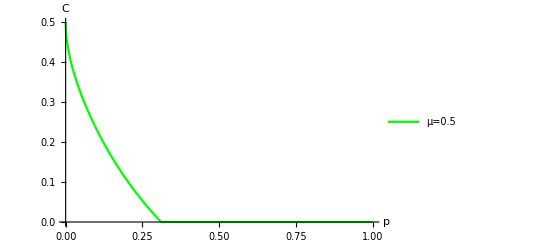

```mathematica
ClearAll[g,γ, μ,  p];
γ=0.5;
g=1/3;
μ=0.5;
p2=Plot[N[concurr[ρ2]],{p,0,1},AxesLabel->{"p","C"},PlotRange->All,PlotLegends->Placed[LineLegend[{"μ=0.5"}],{0.9,0.8}],LabelStyle->{FontSize->10, Black,Bold},PlotRange->{0,0.8}, PlotStyle->Green]
```

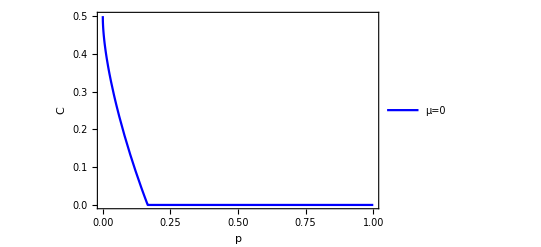

```mathematica
ClearAll[g,γ, μ,  p];
γ=0.5;
g=1/3;
μ=0;
p3=Plot[N[concurr[ρ2]],{p,0,1},AxesLabel->{"p","C"},PlotRange->All,PlotLegends->Placed[LineLegend[{"μ=0"}],{0.9,0.7}],PlotStyle->{Blue},Frame->True, FrameLabel-> {"p","C"},FrameStyle->Directive[Black,Bold,12]]
```

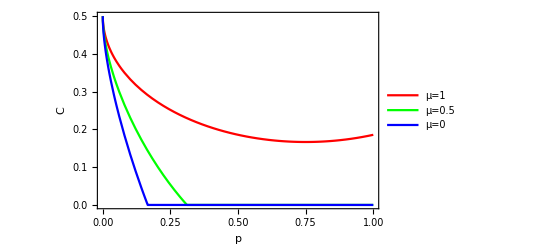

```mathematica
p4=Show[p1,p2,p3, Frame->True, FrameLabel-> {"p","C"},FrameStyle->Directive[Black,Bold,12]]

(* Export the plot to the NotebookDirectory. In the Export[] function, change the figure extension '.pdf' to '.jpg' or '.png' as you need. *)
Export["Conc_DepCh.pdf",p4];
```

```mathematica
(* Concurrence in 3D plot *)
ClearAll[g,γ, μ,  p];
γ=0.5;
g=1/3;
Conc3D=Plot3D[concurr[ρ2],{p,0,1},{μ,0,1},AxesLabel->{"p","μ","C "},AxesStyle->Directive[Bold,Black, 12],ColorFunction->Function[{x,y,z},Hue[Mod[z,1]]],ColorFunctionScaling->False]
(* ColorFunction->Function[{x,y,z},Hue[z]] *)
Export["Conc3D_DepCh.pdf",Conc3D];
```

-Graphics3D-

```mathematica
(* Purity plot in 3D: *)
ClearAll[g,γ,μ,p]
γ=0.5;
g=1/3;
Purity3D=Plot3D[Tr[ρ2.ρ2],{p,0,1},{μ,0,1},PlotRange->All,LabelStyle->Directive[Bold, Medium],AxesLabel->{" p"," μ","Purity  "},ColorFunction->Function[{x,y,z},Hue[Mod[z,1]]],ColorFunctionScaling->False]
(* ColorFunction->Function[{x,y,z},Hue[z]], *)
Export["Purity3D_DepCh.pdf",Purity3D];
```

-Graphics3D-